# Semi-Infinite Rod, Albedo Problem, Anisotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

/Users/eug/Documents/research/hitchhikersscatter

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
g = ‘mean cosine’ of scattering

## Analytic solutions

### Half rod albedo

```mathematica
Clear[α,g];R[α_,g_]:=(α(1-g))/(-α-α g +2 √((1-α)(1-α g))+2)
```

```mathematica
Series[R[α,g],{α,0,3}]
```

(1/4-g/4) α+(1/8-g^2/8) α^2+1/64 (5+g-g^2-5 g^3) α^3+O[α]^4

```mathematica
R[α_,g_,n_]:=α^n(SeriesCoefficient[R[A,g],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
LR[x_,α_,Σt_,g_]:=ⅇ^(- Σt x √((1-α)(1-α g )))
```

```mathematica
LL[x_,α_,Σt_,g_]:=(α(1-g)E^(-Σt x √((1-α)(1-α g ))))/(-α(2 √((1-α g)/(1-α))+g+1)+2(√((1-α g)/(1-α))+1))
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_,g_]:=LR[x,α,Σt,g]+LL[x,α,Σt,g]
```

### n-th collided fluence

```mathematica
ϕ[x_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[ϕ[x,A,Σt,g],{A,0,n}]/.A->α)
```

### moments

## util

```mathematica
ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

## Albedo: variation in g

```mathematica
fsgvariation=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_anisotropicscatter_exp_c0.95_mut1_*"];
```

```mathematica
RMC[filename_]:=Module[{data},
data=Import[filename,"Table"];
{data[[1,-1]],data[[3,3]]}
]
```

```mathematica
gvariationpoints=Table[RMC[f],{f,fsgvariation}];
```

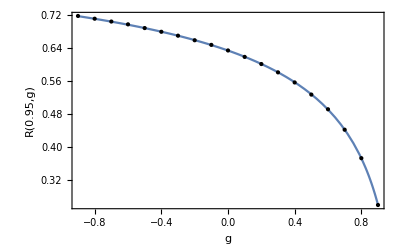

```mathematica
Clear[g];vizgvariation=Show[
Plot[R[0.95,g],{g,-0.9,0.9}],
ListPlot[gvariationpoints,PlotStyle->{PointSize[Medium],Black}],
Frame->True,FrameLabel->{{"R"[0.95,g],},{"g","Total Reflectance/Albedo R(α,g): anisotropically-scattering half rod"}}
]
```

## Monte Carlo vs Analytic

### Select simulation

```mathematica
fs=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_anisotropicscatter_exp*"];
filename=fs[[2]];
data=Import[filename,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];
g=data[[1,-1]];

densmom=data[[11]];
```

### Internal distribution

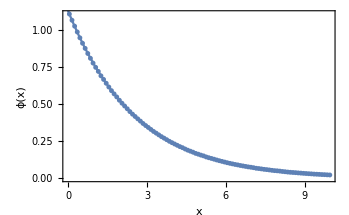

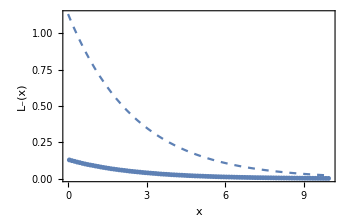

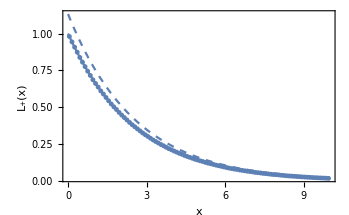

```mathematica
pointsCL = data[[7]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,maxx,Σt];
pointsCR = data[[9]];
plotpointsCR=ppoints[pointsCR,dx,maxx,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}}
]

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt,g],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
]

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt,g],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
]
```

### n-th collided albedo

```mathematica
Rs=N[{data[[5]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[R[α,g,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0. | 0.
1 | 0.0525 | 0.0525077
2 | 0.0312375 | 0.0311924
3 | 0.018731 | 0.0187657
4 | 0.0113172 | 0.0113696
5 | 0.00688819 | 0.0069063
6 | 0.00422229 | 0.0042115
7 | 0.00260578 | 0.0026077
8 | 0.00161856 | 0.001626
9 | 0.00101153 | 0.0010136

### n-th collided radiance/angular flux

ⅇ^-x x (0.0011883+x (0.0011883+x (0.00058963+(0.00019353+0.000621446 x) x)))

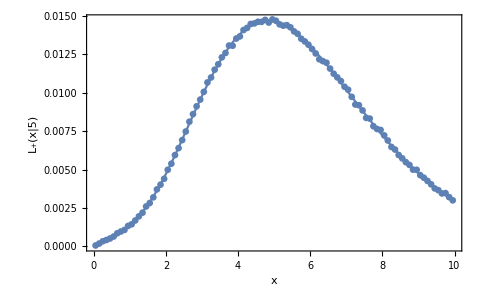

```mathematica
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

(* choose order:*)
n=5;

Clear[c];LnR=FullSimplify[SeriesCoefficient[LR[x,c,Σt,g],{c,0,n}] α^n]
plotLnp=Show[
ListPlot[ppoints[nthR[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LnR,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, anisotropic scattering, L_+[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
]
```

### N-th order Fluence / scalar flux

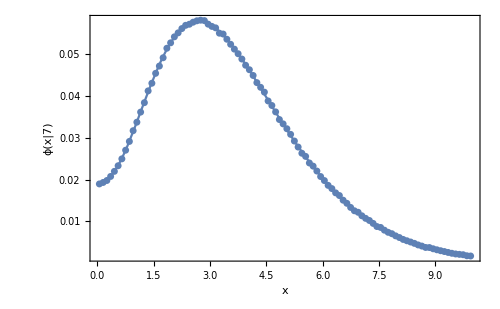

```mathematica
(* choose order:*)
n=3;

Clear[c];
plotphin=Show[
ListPlot[ppoints[nthR[[n+1]]+nthL[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,g,n],{x,0,maxx},PlotRange->All]
,Frame->True,ImageSize->500,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, albedo problem, anisotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
]
```